```mathematica
(*Chris's original plot*)
outputChris=Import["/Users/Frankel/Documents/Files/Onedrive/Ohio_State/Research/Reionization/reionization/output_chris.txt",{"Data",Range[868,1524]}];
marker1=Graphics[{RGBColor[0,0,0.7],Disk[]}];
marker2=Graphics[{RGBColor[50/255,50/255,50/255],Disk[]}];
marker3=Graphics[{RGBColor[0.517,0.651,0.172],Disk[]}];

j=#1&@@@outputChris;
j5DNHI=#2&@@@outputChris;
y1H=#3&@@@outputChris;
y1He=#4&@@@outputChris;
EH=#5&@@@outputChris;
Te=#6&@@@outputChris;

y1H=Transpose[{j5DNHI/10^18,y1H}];
y1He=Transpose[{j5DNHI/10^18,y1He}];
EH=Transpose[{j5DNHI/10^18,EH}];
Te=Transpose[{j5DNHI/10^18,Te/10^4}];
```

```mathematica
label1={{None,Style[ "Neutral fraction",FontSize->24,FontFamily->"Times New Roman"]},{Style["N_H[10^18cm^-2]",FontSize->22,FontFamily->"Times New Roman"],None}};
markers1={{marker1,0.013},{marker2,0.013}};
frame1={True,False,True,True};
ticks1={{None,All},{All,All}};
legend1=Placed[PointLegend[Automatic,{Style["H neutral frac.",FontSize->20,FontFamily->"Times New Roman"],Style["He neutral frac.",FontSize->20,FontFamily->"Times New Roman"]},LegendMarkerSize->10],{0.4,1.0}];

plot1=ListPlot[{y1H,y1He},PlotRange->All,PlotMarkers->markers1,Axes->False,FrameTicks->ticks1,TicksStyle->{FontSize->18,Directive[Thick]}, FrameTicksStyle->FontSize->20,Frame->frame1,FrameStyle->Directive[AbsoluteThickness[1.1],Black],FrameLabel->label1, PlotLegends->legend1,ImagePadding->60,ImageSize->Large]
```

-Graphics-

```mathematica
label2={{Style["Temperature T [10^4K]",FontSize->22,FontFamily->"Times New Roman"],None},{None,None}};
markers2={marker3,0.013};
frame2={False,True,False,False};
ticks2={{All,None},{None,None}};
legend2=Placed[PointLegend[Automatic,{Style["Temperature",FontSize->20,FontFamily->"Times New Roman"],None},LegendMarkerSize->10],{0.766,1.0}];

plot2=ListPlot[{Te,0},PlotRange->All,PlotMarkers->markers2,Axes->False,FrameTicks->ticks2,TicksStyle->{FontSize->18,Directive[Thick]}, FrameTicksStyle->FontSize->20,Frame->frame2,FrameStyle->Directive[AbsoluteThickness[1.1],Black],FrameLabel->label2,PlotLegends->legend2,ImagePadding->60,ImageSize->Large]
```

-Graphics-

```mathematica
Overlay[{plot1,plot2}]
```

-Graphics--Graphics-

```mathematica
(*Chenxiao's Plot*)
ClearAll;
outputChenxiao=Import["/Users/Frankel/Documents/Files/Onedrive/Ohio_State/Research/Reionization/reionization/output_chenxiao1.txt",{"Data",Range[868,1524]}];

marker1=Graphics[{RGBColor[0,0,0.7],Disk[]}];
marker2=Graphics[{RGBColor[50/255,50/255,50/255],Disk[]}];
marker3=Graphics[{RGBColor[0.517,0.651,0.172],Disk[]}];

j=#1&@@@outputChenxiao;
j5DNHI=#2&@@@outputChenxiao;
y1H=#3&@@@outputChenxiao;
y1He=#4&@@@outputChenxiao;
EH=#5&@@@outputChenxiao;
Te=#6&@@@outputChenxiao;
THI=#7&@@@outputChenxiao;
THII=#8&@@@outputChenxiao;
THeI=#9&@@@outputChenxiao;
THeII=#10&@@@outputChenxiao;

y1H=Transpose[{j5DNHI/10^18,y1H}];
y1He=Transpose[{j5DNHI/10^18,y1He}];
EH=Transpose[{j5DNHI/10^18,EH}];
Te=Transpose[{j5DNHI/10^18,Te/10^4}];
THI=Transpose[{j5DNHI/10^18,THI/10^4}];
THII=Transpose[{j5DNHI/10^18,THII/10^4}];
THeI=Transpose[{j5DNHI/10^18,THeI/10^4}];
THeII=Transpose[{j5DNHI/10^18,THeII/10^4}];
```

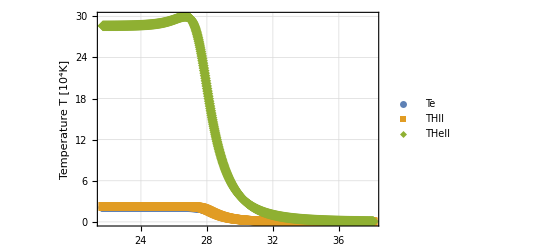

```mathematica
label3={{Style["Temperature T [10^4K]",FontSize->22,FontFamily->"Times New Roman"],None},{None,None}};
markers3={marker3,0.013};
legend3=Placed[PointLegend[Automatic,{Style["Te",FontSize->20,FontFamily->"Times New Roman"],Style["THII",FontSize->20,FontFamily->"Times New Roman"],Style["THeII",FontSize->20,FontFamily->"Times New Roman"],Style["THeI",FontSize->20,FontFamily->"Times New Roman"],Style["THeII",FontSize->20,FontFamily->"Times New Roman"]},LegendMarkerSize->10],Top];
grids[min_,max_]:=Join[Range[Ceiling[min],Floor[max]],Table[{j+.5,Dashed},{j,Round[min],Round[max-1],1}]]

plot3=ListPlot[{Te,THII,THeII},PlotRange->All,PlotMarkers->Automatic,Frame->True,FrameTicks->True,TicksStyle->{FontSize->18,Directive[Thick]}, FrameTicksStyle->FontSize->20,FrameStyle->Directive[AbsoluteThickness[1.1],Black],FrameLabel->label3,PlotLegends->legend3,ImageSize->Full,GridLines->grids]
```